```mathematica
ClearAll["Global`*"]
```

```mathematica
(*kb=1.38064852×10^-23;*)
```

```mathematica
bt=1/(T);
n=10;(*this n should be half of the nCells I used in intellij*)
Ns=2n (2 n +1);(*not sure why's 2n*(2n+1) instead of 2n*2n or (2n-1)(2n-1)*)
x=-bt J;
J=1;
```

I assume G is 1.0  here

## χ from analytical sol from curely

```mathematica
f1=1+8/3 x+32/9 x^2+128/45 x^3;
χ1=Expand[f1*Ns/3 bt]*3
```

3 (-3584/(9 T^4)+4480/(9 T^3)-1120/(3 T^2)+140/T)

### test how Leroyer get χ1 expression

```mathematica
(*L[x_]:=Coth[x]-1/x;
u=L[2x];(*the factor takes into account the definition of the coupling in Rushbrooke's paper*)
w1=(1+u^2)^2+4 u^2;w2=4u(1+u^2);
χ=-x/(6 J)(2 w1+2 w2)/((1-u^2)^2)
Series[%,{x,0,3}]*)
```

```mathematica
(*CoefficientList[-x/(3 J)-(8 x^2)/(9 J)-(32 x^3)/(27 J)+O[x]^4,x]*)
```

```mathematica
u=L[x];(*Just test for not 2x*)
w1=(1+u^2)^2+4 u^2;w2=4u(1+u^2);
χ=-x/(6 J)(2 w1+2 w2)/((1-u^2)^2)
Series[%,{x,0,3}]
```

(8 L[-1/T] (1+L[-1/T]^2)+2 (4 L[-1/T]^2+(1+L[-1/T]^2)^2))/(6 T (1-L[-1/T]^2)^2)

General::ivar: -1/T is not a valid variable.

Series[(8 L[-1/T] (1+L[-1/T]^2)+2 (4 L[-1/T]^2+(1+L[-1/T]^2)^2))/(6 T (1-L[-1/T]^2)^2),{-1/T,0,3}]

```mathematica
χ1/Ns-χ/.T->RandomReal[{1,100}]//N
```

0.0151712-(0.00263753 (8. L[-0.0158252] (1.+L[-0.0158252]^2)+2. (4. L[-0.0158252]^2+(1.+L[-0.0158252]^2)^2)))/(1.-1. L[-0.0158252]^2)^2

It’s the same

## χ from analytical sol from Rushbrooke

```mathematica
f2=1+8/3 x+16/3 x^2+448/45 x^3;
χ2=Expand[f2*Ns/3 bt]
```

-12544/(9 T^4)+2240/(3 T^3)-1120/(3 T^2)+140/T

## Comparison of two method

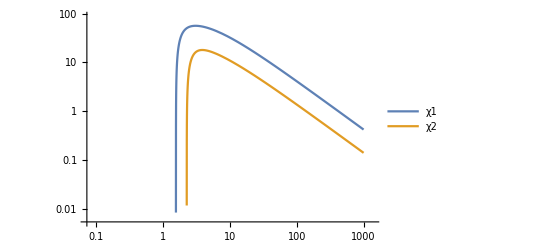

```mathematica
LogLogPlot[{χ1,χ2},{T,0.1,1000},PlotLegends->"Expressions"]
```

## compute lists of value

```mathematica
χ1T[T_]:= χ1/Ns
χ2T[T_]:=-T χ2
```

```mathematica
Collect[- χ1/Ns,T]
```

128/(45 T^4)-32/(9 T^3)+8/(3 T^2)-1/T

```mathematica
T=10;
Solve[((128 J^3)/(45 T^4)-(32 J^2)/(9 T^3)+(8 J)/(3 T^2)-1/T)/T==-0.20616,J]//N
```

{{J→-14.3705},{J→13.4352-17.3028 ⅈ},{J→13.4352+17.3028 ⅈ}}

```mathematica
t1=Table[i*10,{i,1,9}];
t2=Table[i*100,{i,1,9}];
t3=Table[i*500,{i,3,10}];
```

```mathematica
temperature = Flatten[{t1,t2,t3}]
```

{10,20,30,40,50,60,70,80,90,100,200,300,400,500,600,700,800,900,1500,2000,2500,3000,3500,4000,4500,5000}

```mathematica
sus1=Table[N[χ1T[T]],{T,temperature}];
data1=TableForm[ Flatten /@Transpose[{temperature,sus1}]]
Export["~/Dropbox/simulation/heisenberg/chi.dat",data1];
```

10 | 0.0766044
20 | 0.04376
30 | 0.0304985
40 | 0.0233878
50 | 0.0189613
60 | 0.0159422
70 | 0.0137517
80 | 0.0120902
90 | 0.0107867
100 | 0.00973686
200 | 0.00493378
300 | 0.00330384
400 | 0.00248339
500 | 0.00198936
600 | 0.00165928
700 | 0.00142314
800 | 0.00124584
900 | 0.00110782
1500 | 0.000665483
2000 | 0.000499334
2500 | 0.000399574
3000 | 0.000333037
3500 | 0.000285497
4000 | 0.000249833
4500 | 0.000222091
5000 | 0.000199893

## converted value

```mathematica
ClearAll["Global`*"]
```

```mathematica
x=-bt J
```

-bt J

```mathematica
Collect[Solve[3/bt y==1+8/3 x+32/9 x^2+128/45 x^3,y],bt]
```

{{y→bt/3-(8 bt^2 J)/9+(32 bt^3 J^2)/27-(128 bt^4 J^3)/135}}

```mathematica
y[bt_,J_]:=y/.sol[[1]]
```

```mathematica
y[bt,J]/.{bt->1/100,J->0}//N
```

Part::partd: Part specification sol ⟦ 1 ⟧ is longer than depth of object.

ReplaceAll::reps: {sol ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

y/.sol⟦1⟧

```mathematica
128/(135 T^4)-32/(27 T^3)+8/(9 T^2)-1/(3 T)
```

128/(135 T^4)-32/(27 T^3)+8/(9 T^2)-1/(3 T)